# LifeHash

## A beautiful method of hash visualization based on Conway' s Game of Life.

## Latest code available at: https://github.com/wolfmcnally/LifeHash

## by Wolf McNally

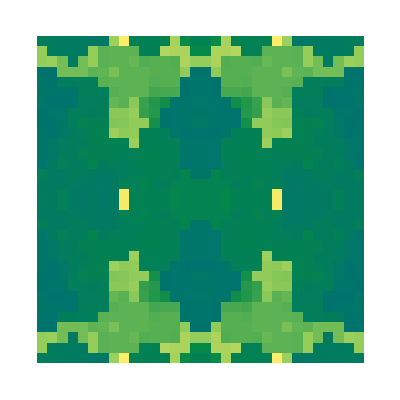

```mathematica
LifeHash["Wolf"]
```

A method of hash visualization based on Conway’s Game of Life that creates beautiful icons that are deterministic, yet distinct and unique given the input data.

The basic concept is to take a SHA256 hash of the input data (which can be any data including another hash) and then use the 256-bit digest as a 16x16 pixel “seed” for running the cellular automata known as Conway’s Game of Life.

After the pattern becomes stable (or begins repeating) the resulting history is used to compile a grayscale image of all the states from the first to last generation. Using Game of Life provides visual structure to the resulting image, even though it was seeded with entropy.

Some bits of the initial hash are then used to deterministically apply symmetry and color to the icon to add beauty and quick recognizability.

## Implementation

```mathematica
CreateHistory[seed_,maxGenerations_]:=Module[{frames,hashes,done,currentFrame,currentHash,gameOfLife},
frames={seed};
hashes={Hash[seed]};
done=False;
gameOfLife=CellularAutomaton["GameOfLife"];
While[!done,
currentFrame=gameOfLife[Last[frames]];
currentHash=Hash[currentFrame];
If[MemberQ[hashes,currentHash],
done=True,
AppendTo[frames,currentFrame];
AppendTo[hashes,currentHash];
If[Length[frames]==maxGenerations,
done=True
];
]
];
frames
];

OverlayFracs[fracArray_,cellArray_,frac_]:= Module[{x,y,result},
result=ConstantArray[0,{16,16}];
For[y=1,y≤16,y++,
For[x=1,x≤16,x++,
result[[y,x]]=If[cellArray[[y,x]]>0,frac,fracArray[[y,x]]]
];
];
result
]

MakeGrays[history_]:=Module[{result,i},
result=ConstantArray[0,{16,16}];
For[i=1,i≤Length[history],i++,
result=OverlayFracs[result,history[[i]],i/N[Length[history]]]
];
result
]

NextInt[entropy_,bitCount_]:={FromDigits[Take[entropy,bitCount],2],Drop[entropy,bitCount]};

NextReal[entropy_,bitCount_]:={N[FromDigits[Take[entropy,bitCount],2]/(2^bitCount-1)],Drop[entropy,bitCount]};

NextFrac[entropy_]:=NextReal[entropy,16]

NextBool[entropy_]:={If[First[entropy]==0,False,True],Rest[entropy]}

spectrumColors=RGBColor@@@N[{{0,168,222},{51,51,145},{233,19,136},{235,45,46},{253,233,43},{0,158,84},{0,168,222}}/255];

SpectrumColor[f_]:=Blend[spectrumColors,f];

Luminance[color_]:=0.2126 color[[1]]+0.7152 color[[2]]+0.0722 color[[3]];

MonochromeGradient[hue_,isTint_,isReversed_,keyAdvance_,neutralAdvance_]:=Module[{keyColor,contrastBrightness,neutralColor,keyColor2,neutralColor2,colors},
keyColor=ColorConvert[Hue[hue,1,1],"RGB"];
If[isTint,
contrastBrightness=1;
keyColor=Darker[keyColor,0.5]
,
contrastBrightness=0;
];
neutralColor=ColorConvert[Hue[0,0,contrastBrightness],"RGB"];
keyColor2=Blend[{keyColor,neutralColor},keyAdvance*0.3+0.05];
neutralColor2=Blend[{neutralColor,keyColor},keyAdvance*0.3+0.05];
colors={keyColor2,neutralColor2};
If[isReversed,colors=Reverse[colors]];
Blend[colors,#]&
];

ComplementaryGradient[spectrum_,lighterAdvance_,darkerAdvance_,isReversed_]:=Module[{spectrum2,color1,color2,darkerColor,lighterColor,adjustedLighterColor,adjustedDarkerColor,colors},
spectrum2=Mod[spectrum+0.5,1];
color1=SpectrumColor[spectrum];
color2=SpectrumColor[spectrum2];
If[Luminance[color1]>Luminance[color2],
darkerColor=color2;
lighterColor=color1;
,
darkerColor=color1;
lighterColor=color2;
];
adjustedLighterColor=Blend[{lighterColor,White},lighterAdvance*0.3];
adjustedDarkerColor=Blend[{darkerColor,Black},darkerAdvance*0.3];
colors={adjustedDarkerColor,adjustedLighterColor};
If[isReversed,colors=Reverse[colors]];
Blend[colors,#]&
];

TriadicGradient[spectrum_,lighterAdvance_,darkerAdvance_,isReversed_]:=Module[{spectrum2,spectrum3,colors,sortedColors,adjustedDarkerColor,adjustedLighterColor},
spectrum2=Mod[spectrum+1/3,1];
spectrum3=Mod[spectrum+2/3,1];
colors={SpectrumColor[spectrum],SpectrumColor[spectrum2],SpectrumColor[spectrum3]};
sortedColors=SortBy[colors,Luminance];
adjustedLighterColor=Blend[{sortedColors[[3]],White},lighterAdvance*0.3];
adjustedDarkerColor=Blend[{sortedColors[[1]],Black},darkerAdvance*0.3];
colors={adjustedLighterColor,sortedColors[[2]],adjustedDarkerColor};
If[isReversed,colors=Reverse[colors]];
Blend[colors,#]&
];

AnalogousGradient[spectrum_,advance_,isReversed_]:=Module[{spectrum2,spectrum3,spectrum4,colors,adjustedAdvance,adjustedDarkestColor,adjustedDarkColor,adjustedLightColor,adjustedLightestColor},
spectrum2=Mod[spectrum+1/12,1];
spectrum3=Mod[spectrum+2/12,1];
spectrum4=Mod[spectrum+3/12,1];
colors=Map[SpectrumColor,{spectrum,spectrum2,spectrum3,spectrum4}];
If[Luminance[colors[[1]]]>Luminance[colors[[4]]],
colors=Reverse[colors]
];
adjustedAdvance=advance*0.5+0.2;
adjustedDarkestColor=Blend[{colors[[1]],Black},adjustedAdvance];
adjustedDarkColor=Blend[{colors[[2]],Black},adjustedAdvance/2];
adjustedLightColor=Blend[{colors[[3]],White},adjustedAdvance/2];
adjustedLightestColor=Blend[{colors[[4]],White},adjustedAdvance];
colors={adjustedDarkestColor, adjustedDarkColor, adjustedLightColor,adjustedLightestColor};
If[isReversed,colors=Reverse[colors]];
Blend[colors,#]&
];

SelectMonochromeGradient[entropy_]:=Module[{ent,hue,isTint,isReversed,keyAdvance,neutralAdvance},
ent=entropy;
{hue,ent}=NextFrac[ent];
{isTint,ent}=NextBool[ent];
{isReversed,ent}=NextBool[ent];
{keyAdvance,ent}=NextFrac[ent];
{neutralAdvance,ent}=NextFrac[ent];
{MonochromeGradient[hue,isTint,isReversed,keyAdvance,neutralAdvance],ent}
];

SelectComplementaryGradient[entropy_]:=Module[{ent,spectrum,lighterAdvance,darkerAdvance,isReversed},
ent=entropy;
{spectrum,ent}=NextFrac[ent];
{lighterAdvance,ent}=NextFrac[ent];
{darkerAdvance,ent}=NextFrac[ent];
{isReversed,ent}=NextBool[ent];
{ComplementaryGradient[spectrum,lighterAdvance,darkerAdvance,isReversed],ent}
];

SelectTriadicGradient[entropy_]:=Module[{ent,spectrum,lighterAdvance,darkerAdvance,isReversed},
ent=entropy;
{spectrum,ent}=NextFrac[ent];
{lighterAdvance,ent}=NextFrac[ent];
{darkerAdvance,ent}=NextFrac[ent];
{isReversed,ent}=NextBool[ent];
{TriadicGradient[spectrum,lighterAdvance,darkerAdvance,isReversed],ent}
];

SelectAnalogousGradient[entropy_]:=Module[{ent,spectrum,advance,isReversed},
ent=entropy;
{spectrum,ent}=NextFrac[ent];
{advance,ent}=NextFrac[ent];
{isReversed,ent}=NextBool[ent];
{AnalogousGradient[spectrum,advance,isReversed],ent}
];

SelectGradient[entropy_]:=Module[{ent,value,colorFunc,type},
ent=entropy;
{value,ent}=NextInt[ent,2];
Switch[value,
0,{colorFunc,ent}=SelectMonochromeGradient[ent];type="monochrome",
1,{colorFunc,ent}=SelectComplementaryGradient[ent];type="complementary",
2,{colorFunc,ent}=SelectTriadicGradient[ent];type="triadic",
3,{colorFunc,ent}=SelectAnalogousGradient[ent];type="analogous"
];
{colorFunc,type,ent}
];

SelectSymmetry[entropy_]:=Module[{ent,value,pattern},
ent=entropy;
{value,ent}=NextBool[ent];
pattern=If[value,"snowflake","pinwheel"];
{pattern,ent}
];

Transform[transpose_,reflectX_,reflectY_]:=Module[{resultX,resultY},
Function[{x,y},
If[transpose,{resultX,resultY}={y,x},{resultX,resultY}={x,y}];
If[reflectX,resultX=32-(resultX-1)];
If[reflectY,resultY=32-(resultY-1)];
{resultX,resultY}
]
];

ClearAll[SetPosition];
SetAttributes[SetPosition,HoldFirst];
SetPosition[array_,{x_,y_},value_]:=array[[y,x]]=value

snowflakeTransforms={
Transform[False,False,False],
Transform[False,True,False],
Transform[False,False,True],
Transform[False,True,True]
};

pinwheelTransforms={
Transform[False,False,False],
Transform[True,True,False],
Transform[True,False,True],
Transform[False,True,True]
};

ApplySymmetry[grays_,pattern_]:=Module[{transforms,result,x,y},
transforms=Switch[pattern,
"snowflake",snowflakeTransforms,
"pinwheel",pinwheelTransforms
];
result=ConstantArray[0,{32,32}];
For[y=1,y≤16,y++,
For[x=1,x≤16,x++,
Map[SetPosition[result,#[x,y],grays[[y,x]]]&,transforms];
];
];
result
];

Fingerprint[value_]:=Module[{hash,binaryDigits,seed,history,grays,entropy,colorFunc,colorFuncType,pattern,symmetryGrays},
hash=Hash[value,"SHA256"];
binaryDigits=IntegerDigits[hash,2,256];
seed=Partition[binaryDigits,16];
history=CreateHistory[seed,150];
entropy=binaryDigits;
{colorFunc,colorFuncType,entropy}=SelectGradient[entropy];
{pattern,entropy}=SelectSymmetry[entropy];
grays=MakeGrays[history];
symmetryGrays=ApplySymmetry[grays,pattern];
{grays,symmetryGrays,colorFunc,pattern}
];

LifeHash[value_]:=Module[{grays,symmetryGrays,colorFunc,pattern},
{grays,symmetryGrays,colorFunc,pattern}=Fingerprint[value];
ArrayPlot[symmetryGrays,ColorFunction->colorFunc]
]
```

## Walkthrough

## Perform a SHA256 hash of the data. If the data is a string, use its UTF-8 encoding.

In this case, we hash the string literal “0”.

```mathematica
hash=Hash["0","SHA256"]
```

43388321209941149759420236104888244958223766953174235657296806338137402595305

## Create a 16x16 seed from the 256 bits of the hash.

```mathematica
binaryDigits=IntegerDigits[hash,2,256]
```

{0,1,0,1,1,1,1,1,1,1,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,1,1,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,1,0,0,0,1,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,0,0,0,1,1,0,1,1,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,0,0,1,0,0,0,1,1,0,1,1,0,1,0,0,0,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0,0,1,1,1,0,1,0,0,0,1,0,0,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,0,1,1,1,1,1,1,0,1,0,0,1}

```mathematica
seed=Partition[binaryDigits,16]
```

{{0,1,0,1,1,1,1,1,1,1,1,0,1,1,0,0},{1,1,1,0,1,0,1,1,0,1,1,0,0,1,1,0},{1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,0},{0,1,1,0,1,1,1,1,0,0,1,1,1,0,0,0},{1,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0},{0,1,1,1,1,0,0,0,0,1,1,0,1,1,0,0},{0,1,1,0,1,1,0,1,0,1,1,0,1,0,0,1},{0,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1},{1,1,0,0,0,0,1,0,1,1,0,1,1,0,1,1},{1,1,0,0,0,0,1,0,0,0,1,1,1,0,0,1},{1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0},{1,0,0,1,0,0,0,1,1,0,1,1,0,1,0,0},{0,1,1,0,0,1,1,1,0,0,1,0,1,0,0,1},{1,1,0,1,0,1,1,1,0,0,1,1,1,0,1,0},{0,0,1,0,0,1,1,1,1,1,1,1,1,0,1,1},{0,1,0,1,0,1,1,1,1,1,1,0,1,0,0,1}}

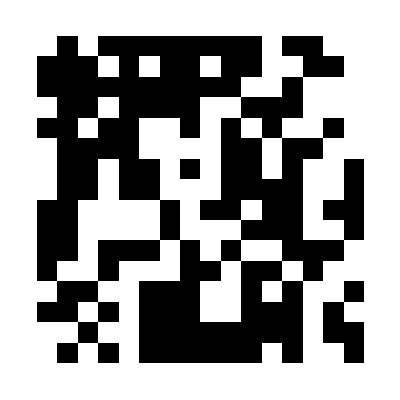

```mathematica
ArrayPlot[seed]
```

## Run Conway’s Game of Life until the pattern either repeats or until 150 generations.

This example runs it for one generation.

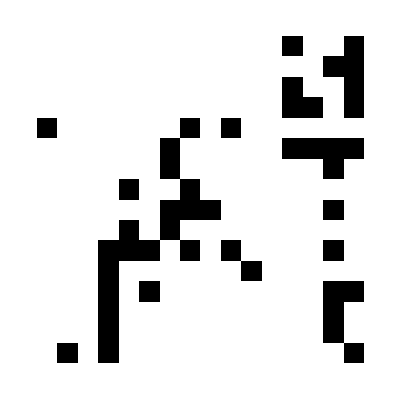

```mathematica
ArrayPlot[CellularAutomaton["GameOfLife",seed]]
```

The complete history for this seed has 69 generations until it stablizies (including the seed.)

```mathematica
history=CreateHistory[seed,150];
```

```mathematica
Length[history]
```

69

```mathematica
Animate[ArrayPlot[history[[i]]],{i,1,Length[history],1},AnimationRunning->False,DisplayAllSteps->True]
```

## Create a “fingerprint” of the history by overlaying all the generations.

```mathematica
Image3D[history,"Bit",BoxRatios->{16, 16, Length[history]}]
```

-Graphics3D-

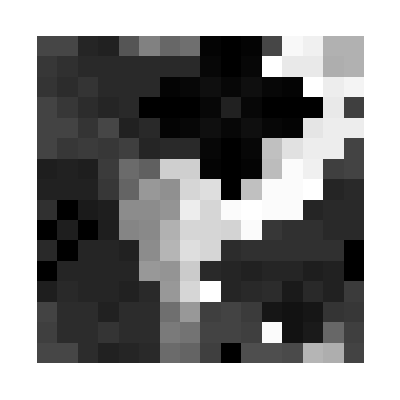

```mathematica
ArrayPlot[Fingerprint["0"][[1]]]
```

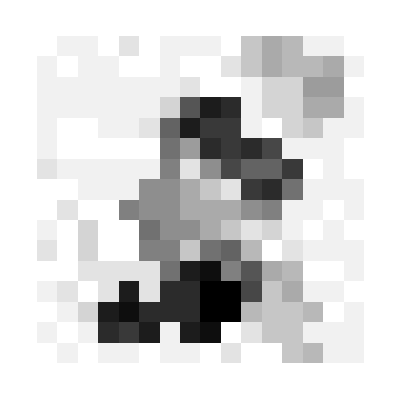
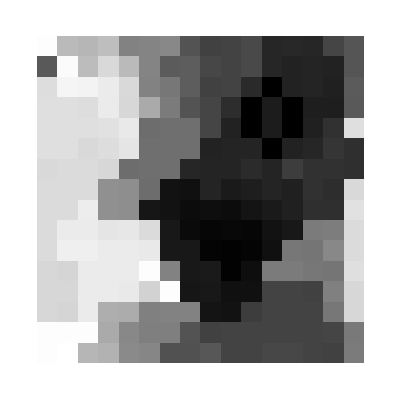
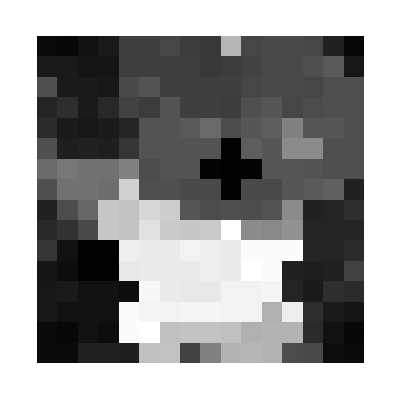
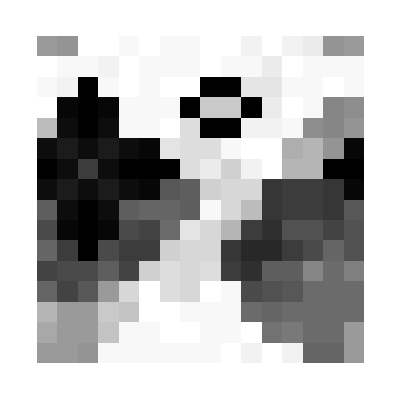
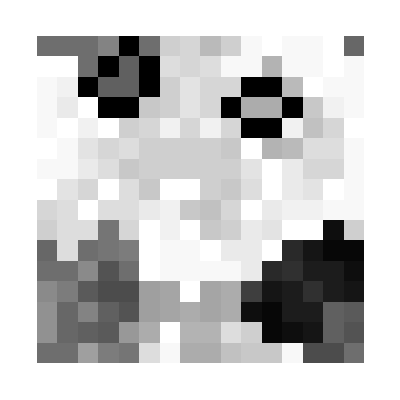
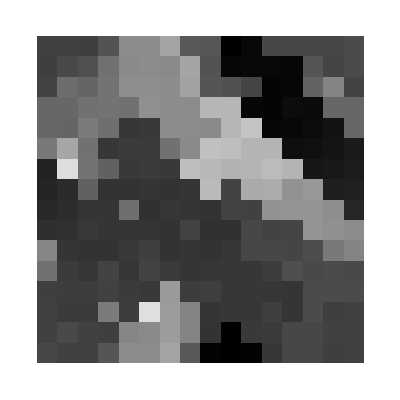
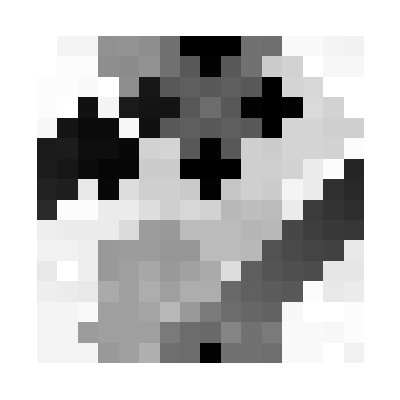
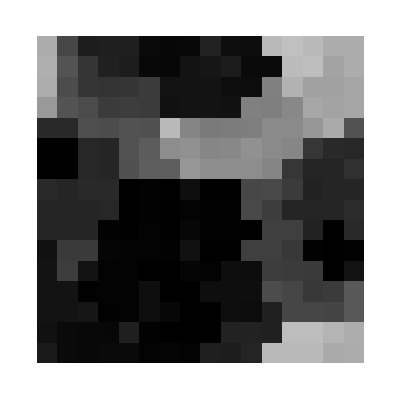
-Graphics-
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4
-Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9
-Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14
-Graphics-
15 | -Graphics-
16 | -Graphics-
17 | -Graphics-
18 | -Graphics-
19
-Graphics-
20 | -Graphics-
21 | -Graphics-
22 | -Graphics-
23 | -Graphics-
24

```mathematica
Grid[
Partition[
Table[Module[{s},
s=ToString[i];
Column[{ArrayPlot[Fingerprint[s][[1]]],s},Center]
],{i,0,24}],5],Spacings->{2,2}
]
```

## Pick a color scheme and symmetry pattern deterministically using bits of the original hash

```mathematica
LinearGradientImage[SpectrumColor]
```

-Graphics-

```mathematica
RandomEntropy[]:=Table[RandomInteger[],256];
ColorSchemeSamples[selectFunc_]:=Table[LinearGradientImage[selectFunc[RandomEntropy[]][[1]],{100,50}],10];
```

```mathematica
ColorSchemeSamples[SelectMonochromeGradient]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorSchemeSamples[SelectComplementaryGradient]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorSchemeSamples[SelectTriadicGradient]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorSchemeSamples[SelectAnalogousGradient]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorSchemeSamples[SelectGradient]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## The finished visual hash, given the same input, should appear the same on every platform.

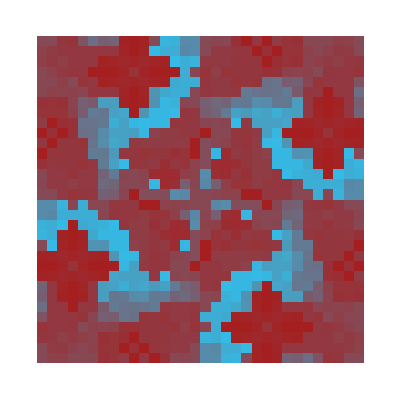
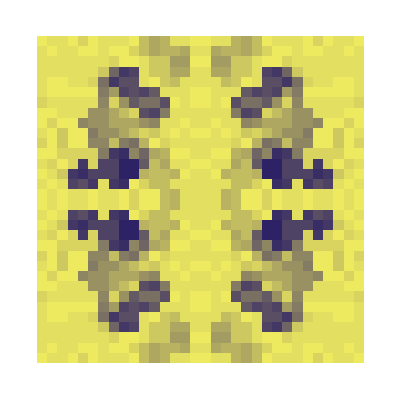
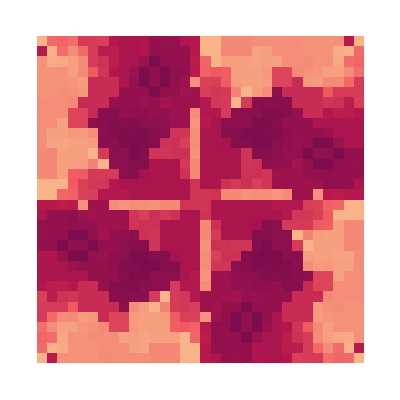
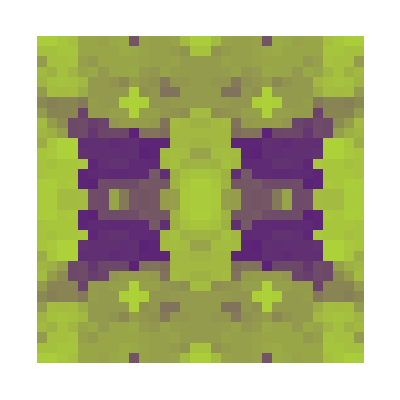
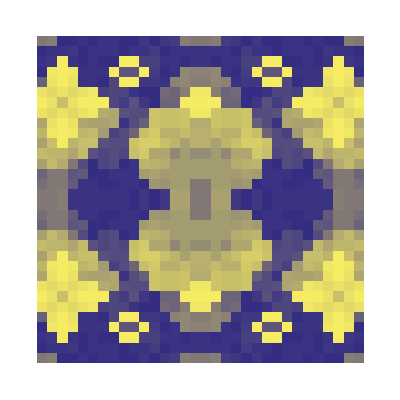
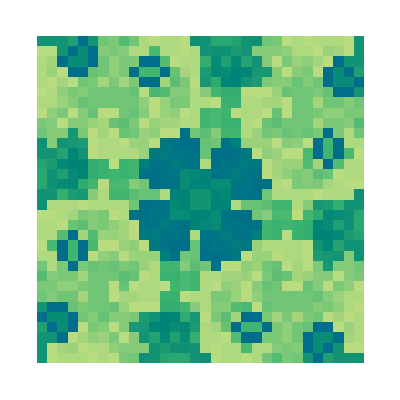
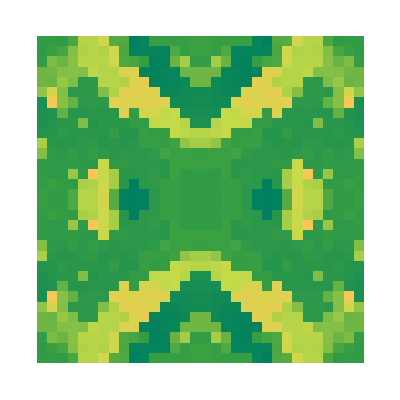
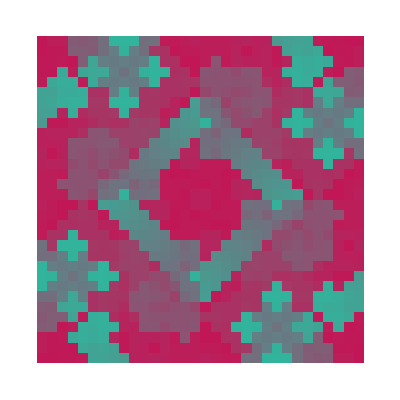
-Graphics-
0 | -Graphics-
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4
-Graphics-
5 | -Graphics-
6 | -Graphics-
7 | -Graphics-
8 | -Graphics-
9
-Graphics-
10 | -Graphics-
11 | -Graphics-
12 | -Graphics-
13 | -Graphics-
14
-Graphics-
15 | -Graphics-
16 | -Graphics-
17 | -Graphics-
18 | -Graphics-
19
-Graphics-
20 | -Graphics-
21 | -Graphics-
22 | -Graphics-
23 | -Graphics-
24
-Graphics-
25 | -Graphics-
26 | -Graphics-
27 | -Graphics-
28 | -Graphics-
29

```mathematica
Grid[
Partition[
Table[Module[{s},
s=ToString[i];
Column[{LifeHash[s],s},Center]
],{i,0,29}],5],Spacings->{2,2}
]
```